# CITS2401 Mathematica assigment Semester 2, 2014 Due : 31/10/2014 by 5 pm

## You are asked to complete the following problems within this mathematica file. On LMS submit 2 files: (1) the original Mathematica file. (2) a pdf of this document. All working/calculations etc should be visible in both files. Save your files using your name and student number.

## Question 1 (4 marks)

At day 0, there are n0 flies in an otherwise unpopulated forest. Each fly produces r offspring per day, but the environment only has enough food for k flies. Their population n[t] on day t is governed by the logistic growth equation:

dn/dt=r n(1-n/k)                            (1)

r is called the growth rate, and k is called the carrying capacity.

(a) Find the symbolic solution of this ordinary differential equation, using the initial condition n = n0 at t = 0. (2 marks)

```mathematica
DSolve[{n'[t] == r * n[t] *(1 - n[t] / k), n[0] == n0 },n[t], t]
```

{{n(t)→(k n0 ⅇ^(r t))/(k+n0 ⅇ^(r t)-n0)}}

(b) If k = 100, n0 = 1 and r = 0.1, how long is it until there are 50 flies? (2 marks)

```mathematica
k = 100
```

```mathematica
n0 = 1
```

```mathematica
r = 0.1
```

```mathematica
Out[8]
```

```mathematica
{{n[t]->(100 ⅇ^(0.1 t))/(99+ⅇ^(0.1 t))}}
```

```mathematica
Solve[(100 * E^(0.1*t))/(99+E^(0.1*t)) == 50, t]
```

{{t→45.9512}}

## Question 2 (4 marks)

A fixed population of birds discovers the forest and feasts on the helpless flies every day, eating up to a maximum number of flies m. The flies’ population model is now

dn/dt=r n(1-n/k)-(m  (n/a)^2)/(1+(n/a)^2)                    (2)

(a) On one graph, plot the new predation term (2nd term on right hand side of equation (2)) between n = 0 and n = 100 with m = 5 and a = 1, 10, 20, 50. Remember to label your axes and include a descriptive legend, and make sure the whole axis is shown.

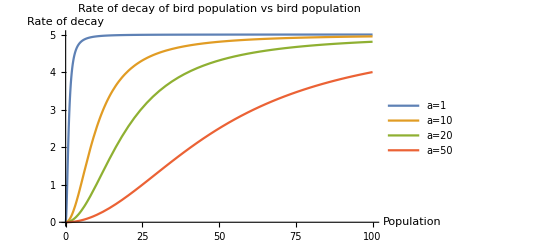

```mathematica
Plot[{(5*(n/1)^2)/(1+(n/1)^2),(5*(n/10)^2)/(1+(n/10)^2),(5*(n/20)^2)/(1+(n/20)^2),(5*(n/50)^2)/(1+(n/50)^2)},{n,0,100},PlotLegends->{"a=1","a=10","a=20","a=50"},PlotLabel->"Rate of decay of bird population vs bird population",AxesLabel->{"Population","Rate of decay"}]
```

(b) Solve equation (2) numerically between t = 0 and t = 100, using the initial condition n = 1 at t = 0 and the parameter values r = 0.1, k = 100, m = 5 and a = 20. Plot your solution on axes between n = 0 and n = 100, and with appropriate labels.

```mathematica
r = 0.1
```

0.1

```mathematica
k = 100
```

100

```mathematica
m = 5
```

5

```mathematica
a = 20
```

20

```mathematica
DSolve[{n'[t] == r*n[t]*(1-n[t]/k)-(m*(n[t]/a)^2)/(1+(n[t]/a)^2),n[0]== 1},n[t],t]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

General::stop: Further output of Solve :: inex will be suppressed during this calculation.

```mathematica
NDSolve[0.01 ((-0.20382822255582006-1.0591766239496603 ⅈ) Log[(-45.65893724366153-50.223781238866906 ⅈ)+n[t]]-(0.20382822255582006-1.0591766239496603 ⅈ) Log[(-45.65893724366153+50.223781238866906 ⅈ)+n[t]]+1.40765644511164 Log[-8.682125512676926+n[t]])-0.01 Log[n[t]]==(-0.03712418783597491+0.044222831467410524 ⅈ)-0.001 t,n[t]]
```

NDSolve::argm: NDSolve called with 2 arguments; 3 or more arguments are expected.

NDSolve[0.01 ((-0.203828-1.05918 ⅈ) Log[(-45.6589-50.2238 ⅈ)+n[t]]-(0.203828-1.05918 ⅈ) Log[(-45.6589+50.2238 ⅈ)+n[t]]+1.40766 Log[-8.68213+n[t]])-0.01 Log[n[t]]==(-0.0371242+0.0442228 ⅈ)-0.001 t,n[t]]

```mathematica
Plot[{Out[48]}, {t,0,100}]
```

-Graphics-

## Question 3 (4 marks)

A criticism of the model in Question 1 is that it is continuous in time, when animals actually reproduce in discrete events. The equivalent discrete logistic growth model is

```mathematica
Subscript[n, t+1]=Subscript[n, t]+r Subscript[n, t](1-Subscript[n, t]/k)                    (3)
```

(a) Using n_0=1 and k = 100, generate a list of the populations on days 1 through 200 when r = 0.1. Plot this list on axes between n = 0 and n = 100, labelling the plot appropriately. (3 marks)
(Hint: Look up the functions NestList and ListPlot.)

```mathematica
NestList[]
```

(b) Make similar plots for each of r = 2.1, r = 2.5 and r = 2.56. What's is happening to the fly population as r is increasing? (1 marks)